```mathematica
f[x_]:=√x;
x={100,144.};
Print["x= ", x];
y=Table[f[x_[[i]]], {i, 1, 2}];
Print["y= ", y];
x=.
Print["Втората производна е: ", D[f[x], x,x]]
```

x= {100,144.}

y= {10,12.}

Втората производна е: -1/(4 x^(3/2))

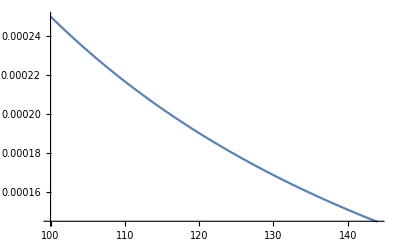

```mathematica
f2[x_]:=Abs[-1/(4 x^(3/2))]
Plot[f2[x], {x, 100, 144}]
```

```mathematica
m3=f2[100.];
xx=121;
Print["Мах на втората производна в случая е при x=100: M3= ", m3]
gr=m3*Abs[{xx-100.}*{xx-144.}]/(2!);
Print["Теоретичната грешка е= ", gr]
```

Мах на втората производна в случая е при x=100: M3= 0.00025

Теоретичната грешка е= {0.060375}